```mathematica
Quit[]
```

#### Kernels Control

```mathematica
LaunchKernels[4]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local]}

```mathematica
CloseKernels[Kernels[]]
```

```mathematica
Kernels[]
```

### Main

#### Declaration

```mathematica
ParallelEvaluate[Off[General::stop]];
```

```mathematica
ParallelEvaluate[On[General::stop]];
```

```mathematica
If[$OperatingSystem == "Windows", {dir = "D:/Documents/2-d-data";}, {dir = "~/Documents/2-d-data";}];
```

The amplitude

```mathematica
MVG[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=If[ω2>ω1,4 g^2 ω1 NIntegrate[1/(1+y ω1-x+ω2-ω1)^2 ϕ1[x/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[1+((y-1)ω1)/ω2],{x,0,1},{y,0,1}],4 g^2 ω2(1+ω2-ω1) NIntegrate[1/(1+y ω2-x(ω1-ω2-1))^2 ϕ1[x]ϕ2[1+(y-1)ω2/ω1]ϕ3[x(1+ω2-ω1)]ϕ4[y],{x,0,1},{y,0,1}]]
```

```mathematica
MHG[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=If[ω2>ω1,4 g^2 ω1 NIntegrate[1/(y ω1-ω2-x)^2 ϕ1[(ω2-ω1+x)/(ω2-ω1+1)]ϕ2[y]ϕ3[x]ϕ4[(y ω1)/ω2],{x,0,1},{y,0,1}],4 g^2 ω2(1+ω2-ω1) NIntegrate[1/(y ω2-x(1+ω2-ω1)-ω1)^2 ϕ1[x]ϕ2[(y ω2)/ω1]ϕ3[ω1-ω2+(1-ω1+ω2)x]ϕ4[y],{x,0,1},{y,0,1}]]
```

Solve ‘t Hooft equation

```mathematica
Clear[m1,m2,β,Nx]; (*β=1 unit*)
Nx=500;(*the size of the working matrix*)
β=1; (*the mass unit,definition β^2=g^2/(2Pi)Nc*)
(*m1=3.2*β;(*m1 and m2 are the bare masses of the quark and the anti-quark.*)
m2=3.2*β;*)
```

```mathematica
Nc=1000;ℂ=0;(*ℂ denotes the interchange of final states.*)λ=10^-6;g=1;
```

```mathematica
vMatx[n_,m_]:=(vMatx[n-1,m-1] m/(m-1)+(8m)/(n+m-1)((1+(-1)^(n+m))/2))
vMatx[1,m_]:=4(1+(-1)^(m+1));
vMatx[n_,1]:=4/n(1+(-1)^(n+1));
```

```mathematica
Determineϕx[m1_,m2_,β_,Nx_]:=
Module[{HMatx,VMatx,vals,vecs,g,ϕx,ϕ},
SetSharedVariable[vecs,m1,m2,β,g];
SetSharedFunction[g];
HMatx=ParallelTable[4Min[n,m]((-1)^(n+m)(m1^2-β^2)+(m2^2-β^2)),{n,1,Nx},{m,1,Nx}];
VMatx=ParallelTable[vMatx[n,m],{n,1,Nx},{m,1,Nx}];
{vals,vecs}=Eigensystem[N[HMatx+VMatx]];
Do[g[j]=Dot[ParallelTable[Sin[i ArcCos[2x-1]],{i,1,Nx}],vecs[[j]]],{j,1,Nx}];
ϕx=ParallelTable[Quiet[g[Nx-n]/√NIntegrate[g[Nx-n]^2,{x,0,1}]],{n,0,20}];
Clear[g];
{√Reverse[vals] β,ϕx}
]
```

```mathematica
ϕn[n_][ϕ_][x_]:=ϕ[x][[n+1]];
```

```mathematica
Mn[n_][vals_]:=vals[[n+1]];
```

Used z=(r_(2-))/(r_(1-)+r_(2-)), ω=(r_(4-))/(r_(1-)+r_(2-)), ω_1=(r_(2-))/(r_(3-)), ω_2=(r_(4-))/(r_(3-)) here.

```mathematica
ωfp[z_][M1_,M2_,M3_,M4_]:=(-√((M1^2 z-M2^2 z+M2^2+M3^2 z^2-M3^2 z-M4^2 z^2+M4^2 z)^2-4 (M4^2 z^2-M4^2 z) (M1^2 (-z)+M2^2 z-M2^2))+M1^2 (-z)+M2^2 z-M2^2-M3^2 z^2+M3^2 z+M4^2 z^2-M4^2 z)/(2 (M1^2 (-z)+M2^2 z-M2^2))(*transform z to ω (Barbon), solution 1.*)
```

```mathematica
ωfn[z_][M1_,M2_,M3_,M4_]:=(√((M1^2 z-M2^2 z+M2^2+M3^2 z^2-M3^2 z-M4^2 z^2+M4^2 z)^2-4 (M4^2 z^2-M4^2 z) (M1^2 (-z)+M2^2 z-M2^2))+M1^2 (-z)+M2^2 z-M2^2-M3^2 z^2+M3^2 z+M4^2 z^2-M4^2 z)/(2 (M1^2 (-z)+M2^2 z-M2^2))(*transform z to ω (Barbon), solution 2*)
```

```mathematica
ω2p[ω1_][M1_,M2_,M3_,M4_]:=1/(2 (M3^2 ω1-M2^2))(-√((M1^2 (-ω1)+M2^2 ω1-M2^2-M3^2 ω1^2+M3^2 ω1+M4^2 ω1)^2-4 (M4^2 ω1-M4^2 ω1^2) (M3^2 ω1-M2^2))+M1^2 ω1-M2^2 ω1+M2^2+M3^2 ω1^2-M3^2 ω1-M4^2 ω1)(*transform ω1 to ω2, your definition, solution 1*)
```

```mathematica
ω2n[ω1_][M1_,M2_,M3_,M4_]:=1/(2 (M3^2 ω1-M2^2))(√((M1^2 (-ω1)+M2^2 ω1-M2^2-M3^2 ω1^2+M3^2 ω1+M4^2 ω1)^2-4 (M4^2 ω1-M4^2 ω1^2) (M3^2 ω1-M2^2))+M1^2 ω1-M2^2 ω1+M2^2+M3^2 ω1^2-M3^2 ω1-M4^2 ω1);(*transform ω1 to ω2, your definition, solution 2*)
```

```mathematica
Sz[z_][M1_,M2_]:=M1^2/(1-z)+M2^2/z;(*Centre of mass energy*)
```

```mathematica
Sω1[ω1_][M1_,M2_,M3_,M4_]:=(M1^2/(1-ω1+ω2p[ω1][M1,M2,M3,M4])+M2^2/ω1)(1+ω2p[ω1][M1,M2,M3,M4]);
```

```mathematica
zfω1[ω1_][MA_,MB_,MC_,MD_]:=ω1/(1+ω2n[ω1][MA,MB,MC,MD])(*transform ω1 to z, using z=ω1/(1+ω2) and previous result of ω1 to ω2*)
ωfω1[ω1_][MA_,MB_,MC_,MD_]:=(ω2n[ω1][MA,MB,MC,MD])/(1+ω2n[ω1][MA,MB,MC,MD]);
```

```mathematica
ω1fz[z_][M1_,M2_,M3_,M4_]:=-z/(ωfp[z][M1,M2,M3,M4]-1);
ω2fz[z_][M1_,M2_,M3_,M4_]:=(-ωfp[z][M1,M2,M3,M4])/(ωfp[z][M1,M2,M3,M4]-1);(*transform z to ω1 and ω2, using z=ω1/(1+ω2) and previous result of z to ω*)
```

```mathematica
ω1S[s_][M1_,M2_,M3_,M4_]:=(-M1^2+M2^2+s-√s √((M1^4+(M2^2-s)^2-2 M1^2 (M2^2+s))/s))/(M3^2-M4^2+s+√s √((M3^4+(M4^2-s)^2-2 M3^2 (M4^2+s))/s));
ω2S[s_][M1_,M2_,M3_,M4_]:=(-M3^2+M4^2+s-√s √((M3^4+(M4^2-s)^2-2 M3^2 (M4^2+s))/s))/(M3^2-M4^2+s+√s √((M3^4+(M4^2-s)^2-2 M3^2 (M4^2+s))/s));
```

```mathematica
MVGab[mQ_,mq_]:=
Module[{ϕxB,ΦB,ValsB,ϕxπ,Φπ,Valsπ,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,filename,ωnow,m1,m2,M4,ϕ4,ω,ΦBbar},
(*SetSharedVariable[m2,m1];*)
m1=mQ;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determineϕx[m1,m2,β,Nx];
Set@@{ΦB[x_],ϕxB};
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
Set@@{ΦB[x_],ϕxB};
}
];
Set@@{ΦBbar[x_],-ΦB[1-x]};
Print["Wavefunction build complete."];
(*Print[ϕn[#][Φ][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[2];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦBbar]}&[2];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦBbar]}&[0];
Print["M1=",M1,"  M2=",M2,"  M3=",M3,"  M4=",M4];
ParallelTable[ω=ω2p[z][M1,M2,M3,M4];If[ω∈Reals,Print["z=",z,"    ω=",ω];{z,MVG[z,ω][ϕ1,ϕ2,ϕ3,ϕ4]},Print["Overflow: z=",z]],{z,0.1,0.3,0.1}]~Join~ParallelTable[ω=ω2p[z][M1,M2,M3,M4];If[ω∈Reals,Print["z=",z,"    ω=",ω];{z,MVG[z,ω][ϕ1,ϕ2,ϕ3,ϕ4]},Print["Overflow: z=",z]],{z,0.3,0.9,0.005}]~Join~
ParallelTable[ω=ω2p[z][M1,M2,M3,M4];If[ω∈Reals,Print["z=",z,"    ω=",ω];{z,MVG[z,ω][ϕ1,ϕ2,ϕ3,ϕ4]},Print["Overflow: z=",z]],{z,0.9,0.999,0.003}]
]
```

```mathematica
MHGab[mQ_,mq_]:=
Module[{ϕxB,ΦB,ValsB,ϕxπ,Φπ,Valsπ,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,filename,ωnow,m1,m2,M4,ϕ4,ω,ΦBbar},
(*SetSharedVariable[m2,m1];*)
m1=mQ;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determineϕx[m1,m2,β,Nx];
Set@@{ΦB[x_],ϕxB};
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
Set@@{ΦB[x_],ϕxB};
}
];
Set@@{ΦBbar[x_],-ΦB[1-x]};
Print["Wavefunction build complete."];
(*Print[ϕn[#][Φ][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[2];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦBbar]}&[2];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦBbar]}&[0];
Print["M1=",M1,"  M2=",M2,"  M3=",M3,"  M4=",M4];
ParallelTable[ω=ω2p[z][M1,M2,M3,M4];If[ω∈Reals,Print["z=",z,"    ω=",ω];{z,MHG[z,ω][ϕ1,ϕ2,ϕ3,ϕ4]},Print["Overflow: z=",z]],{z,0.1,0.3,0.1}]~Join~ParallelTable[ω=ω2p[z][M1,M2,M3,M4];If[ω∈Reals,Print["z=",z,"    ω=",ω];{z,MHG[z,ω][ϕ1,ϕ2,ϕ3,ϕ4]},Print["Overflow: z=",z]],{z,0.3,0.999,0.003}]
]
```

```mathematica
Msum[mQ_,mq_][n1_,n2_,n3_,n4_]:=
Module[{ϕxB,ΦB,ValsB,ϕxπ,Φπ,Valsπ,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,filename,ωnow,m1,m2,M4,ϕ4,ω1,ω2,ΦBbar,Sen},
(*SetSharedVariable[m2,m1];*)
m1=mQ;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determineϕx[m1,m2,β,Nx];
Set@@{ΦB[x_],ϕxB};
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
Set@@{ΦB[x_],ϕxB};
}
];
Set@@{ΦBbar[x_],-ΦB[1-x]};
Print["Wavefunction build complete."];
(*Print[ϕn[#][Φ][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[n1];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦBbar]}&[n2];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[n3];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦBbar]}&[n4];
Print["M1=",M1,"  M2=",M2,"  M3=",M3,"  M4=",M4];
{{M1,M2,M3,M4},ParallelTable[Sen=Ssqur^2;ω1=ω1S[Sen][M1,M2,M3,M4];ω2=ω2S[Sen][M1,M2,M3,M4];
{Ssqur,MVG[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]+MHG[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]},{Ssqur,M1+M2+0.0001,M1+M2+8,0.1}]}
]
```

#### Calc

```mathematica
Clear["Global`g$*"]
```

```mathematica
Information["Global`g$*"]
```

```mathematica
AppendTo[$Path,NotebookDirectory[]];
Get["TwoFlavour`"]
```

```mathematica
displayfunction1[Msumdat_,{min_,max_}]:=ListPlot[{Select[Re@Msumdat[[2]],#∈Reals&],{{Msumdat[[1,2,1]]+Msumdat[[1,2,2]],Last[Msumdat[[2]]][[2]]},{Msumdat[[1,2,1]]+Msumdat[[1,2,2]],First[Msumdat[[2]]][[2]]}}},PlotRange->{{Msumdat[[1,2,1]]+Msumdat[[1,2,2]]+min,Msumdat[[1,2,1]]+Msumdat[[1,2,2]]+max},All},Joined->True,PlotLabel->"Amp: Threshold: "<>ToString[Msumdat[[1,2,1]]+Msumdat[[1,2,2]]]<>" MeV",ImageSize->Medium,PlotLegends->Placed[LineLegend[{ToString[Msumdat[[1,1,1]]]<>"+"<>ToString[Msumdat[[1,1,2]]]<>"→"<>ToString[Msumdat[[1,1,3]]]<>"+"<>ToString[Msumdat[[1,1,4]]]},LegendLayout->{"Column",1}(*,LegendMarkerSize->20*),LegendMargins->3,LegendFunction->"Frame"],{Right,Top}],Frame->True,FrameLabel->{"MeV","ℳ"},PlotStyle->{{Automatic},{Dotted}}];
displayfunction2[Msumdat_,{min_,max_}]:=ListPlot[{Transpose@{Transpose[Msumdat[[2]]][[1]],(Transpose[Msumdat[[2]]][[2]])^2},{{Msumdat[[1,2,1]]+Msumdat[[1,2,2]],(Last[Msumdat[[2]]][[2]])^2},{Msumdat[[1,2,1]]+Msumdat[[1,2,2]],(First[Msumdat[[2]]][[2]])^2}}},PlotRange->{{Msumdat[[1,2,1]]+Msumdat[[1,2,2]]+min,Msumdat[[1,2,1]]+Msumdat[[1,2,2]]+max},All},Joined->True,PlotLabel->"Amp square: Threshold: "<>ToString[Msumdat[[1,2,1]]+Msumdat[[1,2,2]]]<>" MeV",ImageSize->Medium,PlotLegends->Placed[LineLegend[{ToString[Msumdat[[1,1,1]]]<>"+"<>ToString[Msumdat[[1,1,2]]]<>"→"<>ToString[Msumdat[[1,1,3]]]<>"+"<>ToString[Msumdat[[1,1,4]]]},LegendLayout->{"Column",1}(*,LegendMarkerSize->20*),LegendMargins->3,LegendFunction->"Frame"],{Right,Top}],Frame->True,FrameLabel->{"MeV","|ℳ|^2"},PlotStyle->{{Automatic},{Dotted}}]
```

```mathematica
Clear[ϕx,m2,ϕ,vals,M1,M2,M3,ϕ1,ϕ2,ϕ3];
```

#### 2→2

Two amplitudes separately (note that the horizontal axis is ω1, so it must be transformed into S using function Sω1[ω1][M1,M2,M3,M4]), one convenient way is to use the last line in this section, just don’t do the sum up):

```mathematica
MVGva=MVGab[80,60,1]
```

Wavefunction build complete.

M1=141.057  M2=141.057  M3=140.322  M4=140.322

z=0.1    ω=0.0988464

z=0.2    ω=0.197408

z=0.3    ω=0.295565

z=0.3    ω=0.295565

z=0.33    ω=0.324906

z=0.355    ω=0.349312

z=0.38    ω=0.373669

z=0.405    ω=0.397974

z=0.43    ω=0.422219

z=0.455    ω=0.446397

z=0.48    ω=0.470496

z=0.485    ω=0.475306

z=0.46    ω=0.451223

z=0.435    ω=0.427061

z=0.41    ω=0.402828

z=0.36    ω=0.354187

z=0.335    ω=0.329791

z=0.305    ω=0.300459

z=0.385    ω=0.378535

z=0.49    ω=0.480112

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.465    ω=0.456046

z=0.44    ω=0.431899

z=0.415    ω=0.40768

z=0.39    ω=0.383398

z=0.365    ω=0.359061

z=0.495    ω=0.484914

z=0.34    ω=0.334674

z=0.47    ω=0.460866

z=0.31    ω=0.305352

z=0.445    ω=0.436735

z=0.42    ω=0.412529

z=0.5    ω=0.489712

z=0.395    ω=0.388259

z=0.475    ω=0.465683

z=0.37    ω=0.363932

z=0.345    ω=0.339555

z=0.45    ω=0.441567

z=0.505    ω=0.494507

z=0.315    ω=0.310243

z=0.425    ω=0.417376

z=0.53    ω=0.518414

z=0.4    ω=0.393118

z=0.51    ω=0.499297

z=0.555    ω=0.542202

z=0.375    ω=0.368802

z=0.535    ω=0.523182

z=0.35    ω=0.344434

z=0.58    ω=0.565849

z=0.32    ω=0.315132

z=0.56    ω=0.546943

z=0.515    ω=0.504083

z=0.54    ω=0.527945

z=0.605    ω=0.589329

z=0.585    ω=0.570559

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.565    ω=0.551679

z=0.63    ω=0.612609

z=0.52    ω=0.508865

z=0.61    ω=0.594002

z=0.545    ω=0.532702

z=0.655    ω=0.635647

z=0.59    ω=0.575262

z=0.635    ω=0.617238

z=0.57    ω=0.556408

z=0.325    ω=0.32002

z=0.615    ω=0.598667

z=0.66    ω=0.640221

z=0.525    ω=0.513642

z=0.595    ω=0.579959

z=0.64    ω=0.621856

z=0.55    ω=0.537455

z=0.665    ω=0.644783

z=0.575    ω=0.561132

z=0.62    ω=0.603323

z=0.645    ω=0.626464

z=0.6    ω=0.584648

z=0.68    ω=0.658389

z=0.67    ω=0.649332

z=0.705    ω=0.680761

z=0.625    ω=0.607971

z=0.73    ω=0.702664

z=0.65    ω=0.631061

z=0.685    ω=0.662896

z=0.675    ω=0.653868

z=0.71    ω=0.685183

z=0.755    ω=0.723962

z=0.78    ω=0.744456

z=0.735    ω=0.706978

z=0.805    ω=0.763855

z=0.76    ω=0.728133

z=0.83    ω=0.781701

z=0.69    ω=0.667387

z=0.785    ω=0.748435

z=0.715    ω=0.689585

z=0.855    ω=0.797248

z=0.74    ω=0.711266

z=0.81    ω=0.767567

z=0.835    ω=0.785026

z=0.765    ω=0.73227

z=0.86    ω=0.79998

z=0.79    ω=0.752368

z=0.84    ω=0.788252

z=0.815    ω=0.771213

z=0.72    ω=0.693967

z=0.865    ω=0.802557

z=0.695    ω=0.671862

z=0.745    ω=0.715527

z=0.77    ω=0.736371

z=0.795    ω=0.756251

z=0.845    ω=0.791372

z=0.82    ω=0.774788

z=0.87    ω=0.804961

z=0.875    ω=0.807173

z=0.85    ω=0.794374

z=0.75    ω=0.719759

z=0.8    ω=0.760081

z=0.825    ω=0.778286

z=0.775    ω=0.740434

z=0.725    ω=0.698327

z=0.7    ω=0.67632

z=0.88    ω=0.809172

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.885    ω=0.810932

z=0.89    ω=0.812423

z=0.895    ω=0.81361

z=0.9    ω=0.814452

z=0.9    ω=0.814452

z=0.909    ω=0.814935

z=0.918    ω=0.813762

z=0.924    ω=0.811803

z=0.93    ω=0.808658

z=0.936    ω=0.80404

z=0.942    ω=0.797562

z=0.948    ω=0.788689

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.933    ω=0.806555

z=0.951    ω=0.783127

z=0.939    ω=0.801063

z=0.945    ω=0.793466

z=0.927    ω=0.810395

z=0.921    ω=0.812916

z=0.903    ω=0.814772

z=0.912    ω=0.814751

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.954    ω=0.776656

z=0.96    ω=0.76034

z=0.966    ω=0.738005

z=0.972    ω=0.70684

z=0.978    ω=0.661954

z=0.984    ω=0.594029

z=0.915    ω=0.814366

z=0.906    ω=0.814937

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.957    ω=0.769124

z=0.963    ω=0.750067

z=0.969    ω=0.723766

z=0.975    ω=0.686547

z=0.99    ω=0.482839

z=0.996    ω=0.274688

z=0.981    ω=0.63175

z=0.987    ω=0.545913

z=0.993    ω=0.397115

z=0.999    ω=0.0868413

(0.1 | 2.23772×10^-6
0.2 | 0.0000121274
0.3 | 0.0000492934
0.3 | 0.0000492934
0.305 | 0.0000526729
0.31 | 0.0000562701
0.315 | 0.0000600985
0.32 | 0.000064173
0.325 | 0.000068509
0.33 | 0.0000731232
0.335 | 0.0000780332
0.34 | 0.0000832581
0.345 | 0.0000888178
0.35 | 0.0000947339
0.355 | 0.000101029
0.36 | 0.000107728
0.365 | 0.000114857
0.37 | 0.000122443
0.375 | 0.000130516
0.38 | 0.000139108
0.385 | 0.000148254
0.39 | 0.000157988
0.395 | 0.00016835
0.4 | 0.000179381
0.405 | 0.000191125
0.41 | 0.000203631
0.415 | 0.000216947
0.42 | 0.00023113
0.425 | 0.000246237
0.43 | 0.00026233
0.435 | 0.000279477
0.44 | 0.000297748
0.445 | 0.00031722
0.45 | 0.000337977
0.455 | 0.000360106
0.46 | 0.000383703
0.465 | 0.000408869
0.47 | 0.000435714
0.475 | 0.000464356
0.48 | 0.000494922
0.485 | 0.000527548
0.49 | 0.000562381
0.495 | 0.000599579
0.5 | 0.000639312
0.505 | 0.000681764
0.51 | 0.000727132
0.515 | 0.000775631
0.52 | 0.000827489
0.525 | 0.000882957
0.53 | 0.000942303
0.535 | 0.00100582
0.54 | 0.00107381
0.545 | 0.00114663
0.55 | 0.00122463
0.555 | 0.00130823
0.56 | 0.00139783
0.565 | 0.00149393
0.57 | 0.00159702
0.575 | 0.00170764
0.58 | 0.00182641
0.585 | 0.00195396
0.59 | 0.00209101
0.595 | 0.00223831
0.6 | 0.0023967
0.605 | 0.00256709
0.61 | 0.00275047
0.615 | 0.0029479
0.62 | 0.00316058
0.625 | 0.00338977
0.63 | 0.00363687
0.635 | 0.00390341
0.64 | 0.00419106
0.645 | 0.00450163
0.65 | 0.00483713
0.655 | 0.00519972
0.66 | 0.0055918
0.665 | 0.00601599
0.67 | 0.00647513
0.675 | 0.00697238
0.68 | 0.00751116
0.685 | 0.00809527
0.69 | 0.00872882
0.695 | 0.00941638
0.7 | 0.0101629
0.705 | 0.0109739
0.71 | 0.0118554
0.715 | 0.0128138
0.72 | 0.0138566
0.725 | 0.0149916
0.73 | 0.0162275
0.735 | 0.0175738
0.74 | 0.0190409
0.745 | 0.0206403
0.75 | 0.0223844
0.755 | 0.0242866
0.76 | 0.0263618
0.765 | 0.0286259
0.77 | 0.0310961
0.775 | 0.0337909
0.78 | 0.0367301
0.785 | 0.0399348
0.79 | 0.043427
0.795 | 0.0472239
0.8 | 0.0513663
0.805 | 0.0558604
0.81 | 0.060735
0.815 | 0.0660115
0.82 | 0.0717083
0.825 | 0.0778394
0.83 | 0.084412
0.835 | 0.0914232
0.84 | 0.0988573
0.845 | 0.10668
0.85 | 0.114833
0.855 | 0.123227
0.86 | 0.131736
0.865 | 0.140181
0.87 | 0.148329
0.875 | 0.155878
0.88 | 0.16245
0.885 | 0.167587
0.89 | 0.170718
0.895 | 0.171376
0.9 | 0.168838
0.9 | 0.168838
0.903 | 0.165566
0.906 | 0.16086
0.909 | 0.154653
0.912 | 0.146918
0.915 | 0.137682
0.918 | 0.12704
0.921 | 0.115159
0.924 | 0.102294
0.927 | 0.088777
0.93 | 0.0750184
0.933 | 0.0614794
0.936 | 0.0486404
0.939 | 0.0369507
0.942 | 0.0268033
0.945 | 0.0184316
0.948 | 0.0119276
0.951 | 0.00720543
0.954 | 0.00402984
0.957 | 0.00207037
0.96 | 0.000970967
0.963 | 0.000414285
0.966 | 0.000160994
0.969 | 0.0000573415
0.972 | 0.0000189106
0.975 | 5.8314×10^-6
0.978 | 1.68645×10^-6
0.981 | 4.52932×10^-7
0.984 | 1.10407×10^-7
0.987 | 2.36321×10^-8
0.99 | 4.3707×10^-9
0.993 | 6.15263×10^-10
0.996 | 3.96424×10^-11
0.999 | 9.93905×10^-14)

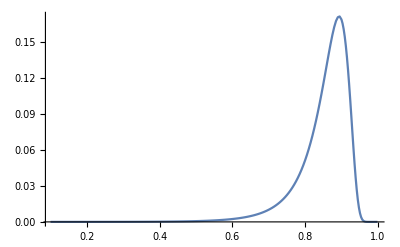

```mathematica
ListPlot[Re[MVGva],PlotRange->All,Joined->True]
ListPlot[Table[{Sω1[x][Msumdat[[1,1]],Msumdat[[1,2]],Msumdat[[1,3]],Msumdat[[1,4]]],Interpolation[MVGva][x]},{x,0.8,0.9,0.001}]]
```

```mathematica
MHGva=MHGab[80,60,1]
```

Wavefunction build complete.

M1=141.057  M2=141.057  M3=140.322  M4=140.322

z=0.1    ω=0.0988464

z=0.2    ω=0.197408

z=0.3    ω=0.295565

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.3    ω=0.295565

z=0.33    ω=0.324906

z=0.36    ω=0.354187

z=0.39    ω=0.383398

z=0.42    ω=0.412529

z=0.45    ω=0.441567

z=0.48    ω=0.470496

z=0.51    ω=0.499297

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.513    ω=0.502169

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.483    ω=0.473382

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.453    ω=0.444465

z=0.423    ω=0.415437

z=0.393    ω=0.386315

z=0.363    ω=0.357111

z=0.333    ω=0.327837

z=0.303    ω=0.298502

z=0.516    ω=0.50504

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.486    ω=0.476267

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.456    ω=0.447362

z=0.426    ω=0.418345

z=0.396    ω=0.389231

z=0.519    ω=0.507909

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.366    ω=0.360035

z=0.336    ω=0.330768

z=0.489    ω=0.479151

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.306    ω=0.301438

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.459    ω=0.450258

z=0.399    ω=0.392146

z=0.522    ω=0.510776

z=0.429    ω=0.421251

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.492    ω=0.482033

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.369    ω=0.362958

z=0.339    ω=0.333697

z=0.462    ω=0.453153

z=0.525    ω=0.513642

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.309    ω=0.304373

z=0.402    ω=0.395061

z=0.432    ω=0.424156

z=0.495    ω=0.484914

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.528    ω=0.516506

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.465    ω=0.456046

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.372    ω=0.36588

z=0.498    ω=0.487794

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.531    ω=0.519368

z=0.342    ω=0.336626

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.435    ω=0.427061

z=0.405    ω=0.397974

z=0.312    ω=0.307308

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.468    ω=0.458939

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.534    ω=0.522229

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.501    ω=0.490672

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.438    ω=0.429964

z=0.375    ω=0.368802

z=0.408    ω=0.400887

z=0.345    ω=0.339555

z=0.471    ω=0.46183

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.537    ω=0.525088

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.315    ω=0.310243

z=0.504    ω=0.493548

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.441    ω=0.432866

z=0.54    ω=0.527945

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.474    ω=0.46472

z=0.378    ω=0.371723

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.507    ω=0.496423

z=0.411    ω=0.403799

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.348    ω=0.342483

z=0.543    ω=0.5308

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.318    ω=0.313177

z=0.444    ω=0.435768

z=0.477    ω=0.467609

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.57    ω=0.556408

z=0.381    ω=0.374643

z=0.414    ω=0.40671

z=0.546    ω=0.533653

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.351    ω=0.34541

z=0.573    ω=0.559243

z=0.447    ω=0.438668

z=0.6    ω=0.584648

z=0.321    ω=0.31611

z=0.549    ω=0.536505

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.576    ω=0.562076

z=0.603    ω=0.587457

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.417    ω=0.40962

z=0.384    ω=0.377562

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.354    ω=0.348336

z=0.552    ω=0.539354

z=0.63    ω=0.612609

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.579    ω=0.564906

z=0.606    ω=0.590264

z=0.633    ω=0.615387

z=0.555    ω=0.542202

z=0.324    ω=0.319043

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.609    ω=0.593068

z=0.66    ω=0.640221

z=0.582    ω=0.567734

z=0.387    ω=0.38048

z=0.636    ω=0.618162

z=0.357    ω=0.351262

z=0.663    ω=0.64296

z=0.558    ω=0.545047

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.612    ω=0.595869

z=0.585    ω=0.570559

z=0.639    ω=0.620933

z=0.666    ω=0.645694

z=0.615    ω=0.598667

z=0.561    ω=0.547891

z=0.327    ω=0.321975

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.642    ω=0.623701

z=0.588    ω=0.573382

z=0.669    ω=0.648423

z=0.69    ω=0.667387

z=0.618    ω=0.601462

z=0.72    ω=0.693967

z=0.645    ω=0.626464

z=0.693    ω=0.670074

z=0.672    ω=0.651148

z=0.564    ω=0.550732

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.591    ω=0.576202

z=0.723    ω=0.696586

z=0.648    ω=0.629224

z=0.696    ω=0.672755

z=0.621    ω=0.604253

z=0.675    ω=0.653868

z=0.726    ω=0.699196

z=0.567    ω=0.553571

z=0.594    ω=0.57902

z=0.75    ω=0.719759

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.699    ω=0.67543

z=0.651    ω=0.63198

z=0.678    ω=0.656582

z=0.729    ω=0.701799

z=0.624    ω=0.607042

z=0.753    ω=0.722285

z=0.702    ω=0.678099

z=0.732    ω=0.704393

z=0.681    ω=0.659291

z=0.78    ω=0.744456

z=0.654    ω=0.634731

z=0.597    ω=0.581835

z=0.756    ω=0.724799

z=0.627    ω=0.609827

z=0.783    ω=0.746849

z=0.735    ω=0.706978

z=0.705    ω=0.680761

z=0.759    ω=0.727301

z=0.684    ω=0.661995

z=0.657    ω=0.637478

z=0.786    ω=0.749226

z=0.738    ω=0.709554

z=0.81    ω=0.767567

z=0.762    ω=0.729792

z=0.708    ω=0.683416

z=0.84    ω=0.788252

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.789    ω=0.751585

z=0.687    ω=0.664694

z=0.813    ω=0.769763

z=0.843    ω=0.790138

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.765    ω=0.73227

z=0.741    ω=0.71212

z=0.867    ω=0.80354

z=0.792    ω=0.753928

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.711    ω=0.686065

z=0.816    ω=0.771934

z=0.846    ω=0.791982

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.87    ω=0.804961

z=0.849    ω=0.793783

z=0.768    ω=0.734735

z=0.894    ω=0.813399

z=0.819    ω=0.774079

z=0.795    ω=0.756251

z=0.873    ω=0.806313

z=0.744    ω=0.714677

z=0.897    ω=0.813991

z=0.852    ω=0.79554

z=0.876    ω=0.807591

z=0.714    ω=0.688706

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.822    ω=0.776197

z=0.9    ω=0.814452

z=0.798    ω=0.758556

z=0.879    ω=0.808791

z=0.855    ω=0.797248

z=0.771    ω=0.737187

z=0.903    ω=0.814772

z=0.747    ω=0.717223

z=0.825    ω=0.778286

z=0.882    ω=0.809906

z=0.858    ω=0.798905

z=0.906    ω=0.814937

z=0.801    ω=0.760841

z=0.717    ω=0.69134

z=0.885    ω=0.810932

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.774    ω=0.739625

z=0.909    ω=0.814935

z=0.861    ω=0.800508

z=0.828    ω=0.780346

z=0.888    ω=0.811861

z=0.912    ω=0.814751

z=0.804    ω=0.763105

z=0.921    ω=0.812916

z=0.864    ω=0.802055

z=0.831    ω=0.782374

z=0.891    ω=0.812686

z=0.915    ω=0.814366

z=0.924    ω=0.811803

z=0.777    ω=0.742048

z=0.948    ω=0.788689

z=0.975    ω=0.686547

z=0.918    ω=0.813762

z=0.927    ω=0.810395

z=0.807    ω=0.765347

z=0.951    ω=0.783127

z=0.978    ω=0.661954

z=0.834    ω=0.784369

z=0.93    ω=0.808658

z=0.954    ω=0.776656

z=0.981    ω=0.63175

z=0.957    ω=0.769124

z=0.933    ω=0.806555

z=0.837    ω=0.786329

z=0.96    ω=0.76034

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

z=0.936    ω=0.80404

z=0.984    ω=0.594029

z=0.963    ω=0.750067

z=0.939    ω=0.801063

z=0.966    ω=0.738005

z=0.987    ω=0.545913

z=0.942    ω=0.797562

z=0.969    ω=0.723766

z=0.945    ω=0.793466

z=0.99    ω=0.482839

z=0.972    ω=0.70684

z=0.993    ω=0.397115

z=0.996    ω=0.274688

z=0.999    ω=0.0868413

(0.1 | 0.0000299283
0.2 | 0.0000795714
0.3 | 0.000196759
0.3 | 0.000196759
0.303 | 0.000202244
0.306 | 0.000207889
0.309 | 0.000213699
0.312 | 0.000219679
0.315 | 0.000225836
0.318 | 0.000232174
0.321 | 0.0002387
0.324 | 0.000245419
0.327 | 0.000252337
0.33 | 0.000259462
0.333 | 0.0002668
0.336 | 0.000274357
0.339 | 0.000282142
0.342 | 0.00029016
0.345 | 0.000298421
0.348 | 0.000306931
0.351 | 0.0003157
0.354 | 0.000324735
0.357 | 0.000334046
0.36 | 0.000343642
0.363 | 0.000353531
0.366 | 0.000363725
0.369 | 0.000374234
0.372 | 0.000385067
0.375 | 0.000396236
0.378 | 0.000407752
0.381 | 0.000419627
0.384 | 0.000431873
0.387 | 0.000444504
0.39 | 0.000457532
0.393 | 0.00047097
0.396 | 0.000484834
0.399 | 0.000499138
0.402 | 0.000513897
0.405 | 0.000529127
0.408 | 0.000544845
0.411 | 0.000561067
0.414 | 0.000577813
0.417 | 0.000595099
0.42 | 0.000612946
0.423 | 0.000631374
0.426 | 0.000650403
0.429 | 0.000670055
0.432 | 0.000690353
0.435 | 0.000711319
0.438 | 0.000732979
0.441 | 0.000755358
0.444 | 0.000778482
0.447 | 0.000802378
0.45 | 0.000827075
0.453 | 0.000852604
0.456 | 0.000878994
0.459 | 0.000906278
0.462 | 0.000934491
0.465 | 0.000963666
0.468 | 0.00099384
0.471 | 0.00102505
0.474 | 0.00105734
0.477 | 0.00109075
0.48 | 0.00112532
0.483 | 0.00116109
0.486 | 0.00119812
0.489 | 0.00123645
0.492 | 0.00127614
0.495 | 0.00131723
0.498 | 0.00135979
0.501 | 0.00140386
0.504 | 0.00144952
0.507 | 0.00149682
0.51 | 0.00154583
0.513 | 0.00159663
0.516 | 0.00164927
0.519 | 0.00170385
0.522 | 0.00176043
0.525 | 0.00181911
0.528 | 0.00187996
0.531 | 0.00194308
0.534 | 0.00200857
0.537 | 0.00207651
0.54 | 0.00214703
0.543 | 0.00222021
0.546 | 0.00229619
0.549 | 0.00237508
0.552 | 0.00245701
0.555 | 0.0025421
0.558 | 0.00263049
0.561 | 0.00272233
0.564 | 0.00281778
0.567 | 0.00291698
0.57 | 0.00302012
0.573 | 0.00312735
0.576 | 0.00323887
0.579 | 0.00335487
0.582 | 0.00347556
0.585 | 0.00360114
0.588 | 0.00373185
0.591 | 0.00386791
0.594 | 0.00400958
0.597 | 0.00415712
0.6 | 0.00431081
0.603 | 0.00447093
0.606 | 0.00463779
0.609 | 0.00481171
0.612 | 0.00499303
0.615 | 0.0051821
0.618 | 0.00537931
0.621 | 0.00558505
0.624 | 0.00579974
0.627 | 0.00602381
0.63 | 0.00625775
0.633 | 0.00650203
0.636 | 0.00675718
0.639 | 0.00702374
0.642 | 0.00730231
0.645 | 0.00759348
0.648 | 0.00789792
0.651 | 0.0082163
0.654 | 0.00854935
0.657 | 0.00889785
0.66 | 0.0092626
0.663 | 0.00964448
0.666 | 0.0100444
0.669 | 0.0104633
0.672 | 0.0109022
0.675 | 0.0113623
0.678 | 0.0118446
0.681 | 0.0123504
0.684 | 0.012881
0.687 | 0.0134378
0.69 | 0.0140222
0.693 | 0.0146358
0.696 | 0.0152804
0.699 | 0.0159575
0.702 | 0.0166692
0.705 | 0.0174173
0.708 | 0.0182041
0.711 | 0.0190318
0.714 | 0.0199028
0.717 | 0.0208197
0.72 | 0.0217852
0.723 | 0.0228023
0.726 | 0.023874
0.729 | 0.0250037
0.732 | 0.026195
0.735 | 0.0274515
0.738 | 0.0287775
0.741 | 0.0301771
0.744 | 0.0316551
0.747 | 0.0332163
0.75 | 0.034866
0.753 | 0.0366099
0.756 | 0.038454
0.759 | 0.0404047
0.762 | 0.0424691
0.765 | 0.0446543
0.768 | 0.0469684
0.771 | 0.0494198
0.774 | 0.0520176
0.777 | 0.0547713
0.78 | 0.0576915
0.783 | 0.0607891
0.786 | 0.0640761
0.789 | 0.067565
0.792 | 0.0712695
0.795 | 0.0752039
0.798 | 0.0793838
0.801 | 0.0838255
0.804 | 0.0885467
0.807 | 0.093566
0.81 | 0.0989034
0.813 | 0.10458
0.816 | 0.110618
0.819 | 0.117041
0.822 | 0.123874
0.825 | 0.131144
0.828 | 0.138878
0.831 | 0.147105
0.834 | 0.155854
0.837 | 0.165156
0.84 | 0.175044
0.843 | 0.185549
0.846 | 0.196704
0.849 | 0.20854
0.852 | 0.221089
0.855 | 0.234379
0.858 | 0.248436
0.861 | 0.263283
0.864 | 0.278937
0.867 | 0.295406
0.87 | 0.31269
0.873 | 0.330775
0.876 | 0.349631
0.879 | 0.36921
0.882 | 0.389436
0.885 | 0.410204
0.888 | 0.431374
0.891 | 0.452759
0.894 | 0.474123
0.897 | 0.495167
0.9 | 0.515525
0.903 | 0.534752
0.906 | 0.552317
0.909 | 0.567601
0.912 | 0.579891
0.915 | 0.588388
0.918 | 0.592221
0.921 | 0.590479
0.924 | 0.582249
0.927 | 0.56669
0.93 | 0.543124
0.933 | 0.511154
0.936 | 0.470802
0.939 | 0.42266
0.942 | 0.36802
0.945 | 0.308949
0.948 | 0.248244
0.951 | 0.189241
0.954 | 0.135411
0.957 | 0.0897856
0.96 | 0.0543315
0.963 | 0.0294809
0.966 | 0.0140694
0.969 | 0.00579218
0.972 | 0.0020246
0.975 | 0.000596573
0.978 | 0.000149125
0.981 | 0.000032164
0.984 | 6.04637×10^-6
0.987 | 9.65031×10^-7
0.99 | 1.18859×10^-7
0.993 | 9.57987×10^-9
0.996 | 4.18683×10^-10
0.999 | 6.90336×10^-13)

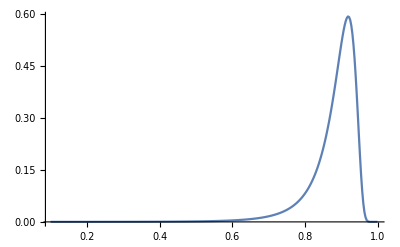

```mathematica
ListPlot[Re[MHGva],PlotRange->All,Joined->True]
```

```mathematica
ListPlot[Table[{Sω1[x],Interpolation[MVGva][x]+Interpolation[MHGva][x]},{x,0,1}]]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

Interpolation::inddp: The point 0.3 in dimension 1 is duplicated.

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

Interpolation::inddp: The point 0.3 in dimension 1 is duplicated.

General::stop: Further output of Interpolation::inddp will be suppressed during this calculation.

-Graphics-

The total amplitude (and the square):

```mathematica
Msumdat=Msum[80,60][2,2,0,0]
```

Wavefunction build complete.

M1=141.057  M2=141.057  M3=140.322  M4=140.322

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{141.057,141.057,140.322,140.322},{{282.114,0.715702},{282.214,0.543116},{282.314,0.446727},{282.414,0.37675},{282.514,0.323116},{282.614,0.280692},{282.714,0.24638},{282.814,0.218151},{282.914,0.1946},{283.014,0.174722},{283.114,0.157775},{283.214,0.143199},{283.314,0.130567},{283.414,0.119543},{283.514,0.109863},{283.614,0.101315},{283.714,0.093728},{283.814,0.0869625},{283.914,0.0809034},{284.014,0.0754553},{284.114,0.0705385},{284.214,0.0660859},{284.314,0.0620407},{284.414,0.0583547},{284.514,0.0549864},{284.614,0.0519005},{284.714,0.0490661},{284.814,0.0464568},{284.914,0.0440492},{285.014,0.0418231},{285.114,0.0397608},{285.214,0.0378465},{285.314,0.0360666},{285.414,0.0344086},{285.514,0.0328618},{285.614,0.0314164},{285.714,0.0300638},{285.814,0.0287962},{285.914,0.0276067},{286.014,0.026489},{286.114,0.0254374},{286.214,0.0244469},{286.314,0.0235128},{286.414,0.0226309},{286.514,0.0217975},{286.614,0.021009},{286.714,0.0202622},{286.814,0.0195544},{286.914,0.0188828},{287.014,0.0182451},{287.114,0.0176389},{287.214,0.0170623},{287.314,0.0165134},{287.414,0.0159904},{287.514,0.0154917},{287.614,0.0150159},{287.714,0.0145616},{287.814,0.0141275},{287.914,0.0137124},{288.014,0.0133152},{288.114,0.012935},{288.214,0.0125708},{288.314,0.0122216},{288.414,0.0118868},{288.514,0.0115655},{288.614,0.0112569},{288.714,0.0109605},{288.814,0.0106756},{288.914,0.0104017},{289.014,0.0101381},{289.114,0.00988434},{289.214,0.00963998},{289.314,0.00940455},{289.414,0.0091776},{289.514,0.00895875},{289.614,0.00874761},{289.714,0.00854383},{289.814,0.00834707},{289.914,0.00815701},{290.014,0.00797335}}}

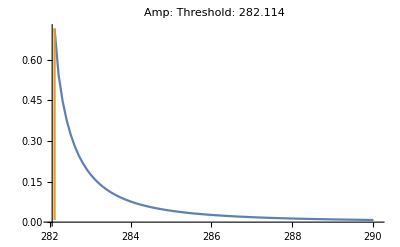

```mathematica
ListPlot[{Select[Re@Msumdat[[2]],#∈Reals&],{{Msumdat[[1,1]]+Msumdat[[1,2]],Last[Msumdat[[2]]][[2]]},{Msumdat[[1,1]]+Msumdat[[1,2]],First[Msumdat[[2]]][[2]]}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,Msumdat[[1,1]]+Msumdat[[1,2]]+8},All},Joined->True,PlotLabel->"Amp: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]]]
```

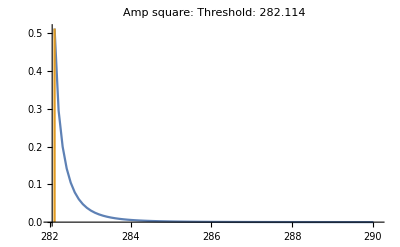

```mathematica
ListPlot[{Transpose@{Transpose[Msumdat[[2]]][[1]],(Transpose[Msumdat[[2]]][[2]])^2},{{Msumdat[[1,1]]+Msumdat[[1,2]],(Last[Msumdat[[2]]][[2]])^2},{Msumdat[[1,1]]+Msumdat[[1,2]],(First[Msumdat[[2]]][[2]])^2}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,Msumdat[[1,1]]+Msumdat[[1,2]]+8},All},Joined->True,PlotLabel->"Amp square: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]]]
```

```mathematica
Msumdat=Msum2[{80,60},{2,2,0,0},SRange->{10^-3,2,0.01}]
```

Wavefunction build complete.

M1=141.057  M2=141.057  M3=140.322  M4=140.322

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{{2,2,0,0},{141.057,141.057,140.322,140.322}},{{282.115,1.43541},{282.125,1.4211},{282.135,1.39874},{282.145,1.37513},{282.155,1.35134},{282.165,1.32773},{282.175,1.3045},{282.185,1.28171},{282.195,1.25942},{282.205,1.23764},{282.215,1.21633},{282.225,1.19565},{282.235,1.17543},{282.245,1.15571},{282.255,1.13648},{282.265,1.11774},{282.275,1.09946},{282.285,1.08163},{282.295,1.06424},{282.305,1.04728},{282.315,1.03073},{282.325,1.01458},{282.335,0.998816},{282.345,0.983428},{282.355,0.968405},{282.365,0.953733},{282.375,0.939403},{282.385,0.925404},{282.395,0.911724},{282.405,0.898356},{282.415,0.885288},{282.425,0.872513},{282.435,0.860021},{282.445,0.847803},{282.455,0.835852},{282.465,0.824159},{282.475,0.812718},{282.485,0.80152},{282.495,0.790558},{282.505,0.779827},{282.515,0.769319},{282.525,0.759027},{282.535,0.748947},{282.545,0.739072},{282.555,0.729396},{282.565,0.719915},{282.575,0.710622},{282.585,0.701512},{282.595,0.692581},{282.605,0.683824},{282.615,0.675236},{282.625,0.666814},{282.635,0.658551},{282.645,0.650445},{282.655,0.642492},{282.665,0.634687},{282.675,0.627027},{282.685,0.619508},{282.695,0.612126},{282.705,0.604879},{282.715,0.597763},{282.725,0.590774},{282.735,0.58391},{282.745,0.577167},{282.755,0.570544},{282.765,0.564036},{282.775,0.557641},{282.785,0.551356},{282.795,0.54518},{282.805,0.539109},{282.815,0.53314},{282.825,0.527273},{282.835,0.521503},{282.845,0.51583},{282.855,0.510251},{282.865,0.504763},{282.875,0.499365},{282.885,0.494055},{282.895,0.488831},{282.905,0.483691},{282.915,0.478633},{282.925,0.473655},{282.935,0.468757},{282.945,0.463935},{282.955,0.459188},{282.965,0.454515},{282.975,0.449915},{282.985,0.445385},{282.995,0.440925},{283.005,0.436532},{283.015,0.432206},{283.025,0.427945},{283.035,0.423747},{283.045,0.419613},{283.055,0.415539},{283.065,0.411525},{283.075,0.407571},{283.085,0.403674},{283.095,0.399833},{283.105,0.396048},{283.115,0.392317},{283.125,0.38864},{283.135,0.385015},{283.145,0.381441},{283.155,0.377917},{283.165,0.374443},{283.175,0.371017},{283.185,0.367639},{283.195,0.364308},{283.205,0.361022},{283.215,0.357781},{283.225,0.354584},{283.235,0.351431},{283.245,0.34832},{283.255,0.345239},{283.265,0.342222},{283.275,0.339234},{283.285,0.336286},{283.295,0.333372},{283.305,0.330505},{283.315,0.327671},{283.325,0.324874},{283.335,0.322113},{283.345,0.319387},{283.355,0.316697},{283.365,0.314041},{283.375,0.311418},{283.385,0.308829},{283.395,0.306272},{283.405,0.303748},{283.415,0.301255},{283.425,0.298792},{283.435,0.29636},{283.445,0.293959},{283.455,0.291587},{283.465,0.289243},{283.475,0.286929},{283.485,0.284642},{283.495,0.282383},{283.505,0.280151},{283.515,0.277946},{283.525,0.275767},{283.535,0.273614},{283.545,0.271487},{283.555,0.269384},{283.565,0.267306},{283.575,0.265253},{283.585,0.263223},{283.595,0.261217},{283.605,0.259234},{283.615,0.257273},{283.625,0.255335},{283.635,0.25342},{283.645,0.251526},{283.655,0.249653},{283.665,0.247801},{283.675,0.245971},{283.685,0.244161},{283.695,0.24237},{283.705,0.2406},{283.715,0.23885},{283.725,0.237118},{283.735,0.235406},{283.745,0.233712},{283.755,0.232037},{283.765,0.23038},{283.775,0.228741},{283.785,0.227119},{283.795,0.225515},{283.805,0.223928},{283.815,0.222358},{283.825,0.220805},{283.835,0.219268},{283.845,0.217747},{283.855,0.216242},{283.865,0.214753},{283.875,0.213279},{283.885,0.211821},{283.895,0.210378},{283.905,0.20895},{283.915,0.207536},{283.925,0.206137},{283.935,0.204752},{283.945,0.203381},{283.955,0.202024},{283.965,0.200681},{283.975,0.199351},{283.985,0.198035},{283.995,0.196731},{284.005,0.195441},{284.015,0.194164},{284.025,0.192899},{284.035,0.191647},{284.045,0.190407},{284.055,0.189179},{284.065,0.187963},{284.075,0.186759},{284.085,0.185566},{284.095,0.184385},{284.105,0.183216}}}

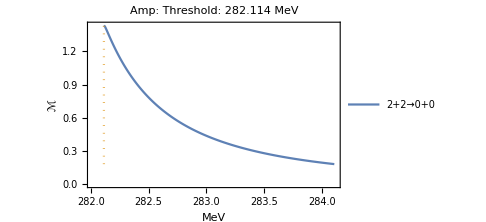
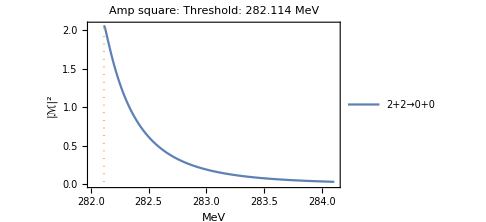

```mathematica
Row[{displayfunction1[Msumdat,{-0.1,2}],displayfunction2[Msumdat,{-0.1,2}]}]
```

```mathematica
Msumdat=Msum2[{80,60},{0,0,0,0},SRange->{10^-3,50,0.5}]
```

Wavefunction build complete.

M1=140.322  M2=140.322  M3=140.322  M4=140.322

{{{0,0,0,0},{140.322,140.322,140.322,140.322}},{{280.645,8.01871},{281.145,7.99202},{281.645,7.96545},{282.145,7.93901},{282.645,7.9127},{283.145,7.88652},{283.645,7.86046},{284.145,7.83453},{284.645,7.80873},{285.145,7.78305},{285.645,7.75749},{286.145,7.73206},{286.645,7.70674},{287.145,7.68155},{287.645,7.65648},{288.145,7.63153},{288.645,7.60669},{289.145,7.58198},{289.645,7.55738},{290.145,7.5329},{290.645,7.50854},{291.145,7.48429},{291.645,7.46016},{292.145,7.43614},{292.645,7.41223},{293.145,7.38843},{293.645,7.36475},{294.145,7.34118},{294.645,7.31772},{295.145,7.29437},{295.645,7.27112},{296.145,7.24799},{296.645,7.22496},{297.145,7.20205},{297.645,7.17923},{298.145,7.15653},{298.645,7.13393},{299.145,7.11143},{299.645,7.08904},{300.145,7.06675},{300.645,7.04456},{301.145,7.02248},{301.645,7.0005},{302.145,6.97861},{302.645,6.95683},{303.145,6.93515},{303.645,6.91357},{304.145,6.89208},{304.645,6.8707},{305.145,6.84941},{305.645,6.82822},{306.145,6.80712},{306.645,6.78612},{307.145,6.76522},{307.645,6.7444},{308.145,6.72369},{308.645,6.70306},{309.145,6.68253},{309.645,6.6621},{310.145,6.64175},{310.645,6.6215},{311.145,6.60133},{311.645,6.58126},{312.145,6.56127},{312.645,6.54138},{313.145,6.52166},{313.645,6.50194},{314.145,6.48222},{314.645,6.46268},{315.145,6.44322},{315.645,6.42385},{316.145,6.40456},{316.645,6.38536},{317.145,6.36624},{317.645,6.34721},{318.145,6.32826},{318.645,6.3094},{319.145,6.29062},{319.645,6.27192},{320.145,6.2533},{320.645,6.23476},{321.145,6.2163},{321.645,6.19793},{322.145,6.17963},{322.645,6.16141},{323.145,6.14328},{323.645,6.12522},{324.145,6.10724},{324.645,6.08933},{325.145,6.07151},{325.645,6.05376},{326.145,6.03608},{326.645,6.01849},{327.145,6.00096},{327.645,5.98352},{328.145,5.96614},{328.645,5.94885},{329.145,5.93162},{329.645,5.91447},{330.145,5.89739}}}

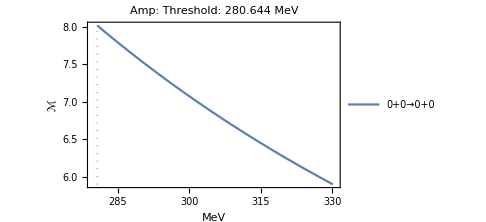
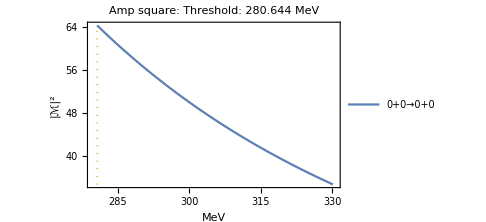

```mathematica
Row[{displayfunction1[Msumdat,{-1,50}],displayfunction2[Msumdat,{-1,50}]}]
```

```mathematica
Msumdat=Msum2[{80,60},{2,0,0,0},SRange->{10^-3,2,0.01}]
```

Wavefunction build complete.

M1=141.057  M2=140.322  M3=140.322  M4=140.322

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{{2,0,0,0},{141.057,140.322,140.322,140.322}},{{281.38,-1.95015},{281.39,-1.89908},{281.4,-1.85473},{281.41,-1.81388},{281.42,-1.77565},{281.43,-1.73963},{281.44,-1.70551},{281.45,-1.67304},{281.46,-1.64208},{281.47,-1.61248},{281.48,-1.58412},{281.49,-1.55691},{281.5,-1.53076},{281.51,-1.5056},{281.52,-1.48136},{281.53,-1.45799},{281.54,-1.43543},{281.55,-1.41363},{281.56,-1.39255},{281.57,-1.37215},{281.58,-1.3524},{281.59,-1.33325},{281.6,-1.31469},{281.61,-1.29667},{281.62,-1.27918},{281.63,-1.26219},{281.64,-1.24568},{281.65,-1.22963},{281.66,-1.21401},{281.67,-1.19881},{281.68,-1.184},{281.69,-1.16958},{281.7,-1.15553},{281.71,-1.14183},{281.72,-1.12847},{281.73,-1.11543},{281.74,-1.10271},{281.75,-1.09029},{281.76,-1.07816},{281.77,-1.06631},{281.78,-1.05473},{281.79,-1.04341},{281.8,-1.03234},{281.81,-1.02151},{281.82,-1.01092},{281.83,-1.00056},{281.84,-0.990413},{281.85,-0.980479},{281.86,-0.970752},{281.87,-0.961222},{281.88,-0.951887},{281.89,-0.942737},{281.9,-0.933768},{281.91,-0.924975},{281.92,-0.916352},{281.93,-0.907894},{281.94,-0.899597},{281.95,-0.891455},{281.96,-0.883465},{281.97,-0.875621},{281.98,-0.867921},{281.99,-0.860359},{282.,-0.852933},{282.01,-0.845638},{282.02,-0.83847},{282.03,-0.831428},{282.04,-0.824506},{282.05,-0.817703},{282.06,-0.811014},{282.07,-0.804438},{282.08,-0.797971},{282.09,-0.79161},{282.1,-0.785353},{282.11,-0.779198},{282.12,-0.773141},{282.13,-0.76718},{282.14,-0.761314},{282.15,-0.755539},{282.16,-0.749854},{282.17,-0.744256},{282.18,-0.738744},{282.19,-0.733316},{282.2,-0.727969},{282.21,-0.722702},{282.22,-0.717512},{282.23,-0.712399},{282.24,-0.707361},{282.25,-0.702395},{282.26,-0.697501},{282.27,-0.692677},{282.28,-0.68792},{282.29,-0.683231},{282.3,-0.678607},{282.31,-0.674047},{282.32,-0.669549},{282.33,-0.665113},{282.34,-0.660737},{282.35,-0.65642},{282.36,-0.652161},{282.37,-0.647958},{282.38,-0.643811},{282.39,-0.639718},{282.4,-0.635678},{282.41,-0.63169},{282.42,-0.627754},{282.43,-0.623867},{282.44,-0.62003},{282.45,-0.616241},{282.46,-0.6125},{282.47,-0.608805},{282.48,-0.605156},{282.49,-0.601551},{282.5,-0.597991},{282.51,-0.594473},{282.52,-0.590998},{282.53,-0.587564},{282.54,-0.584172},{282.55,-0.580819},{282.56,-0.577506},{282.57,-0.574231},{282.58,-0.570995},{282.59,-0.567796},{282.6,-0.564634},{282.61,-0.561507},{282.62,-0.558416},{282.63,-0.55536},{282.64,-0.552339},{282.65,-0.54935},{282.66,-0.546396},{282.67,-0.543473},{282.68,-0.540583},{282.69,-0.537724},{282.7,-0.534896},{282.71,-0.532099},{282.72,-0.529331},{282.73,-0.526594},{282.74,-0.523885},{282.75,-0.521205},{282.76,-0.518552},{282.77,-0.515928},{282.78,-0.513332},{282.79,-0.510761},{282.8,-0.508217},{282.81,-0.505699},{282.82,-0.503206},{282.83,-0.500739},{282.84,-0.498296},{282.85,-0.495879},{282.86,-0.493485},{282.87,-0.491115},{282.88,-0.488768},{282.89,-0.486445},{282.9,-0.484144},{282.91,-0.481865},{282.92,-0.479609},{282.93,-0.477374},{282.94,-0.47516},{282.95,-0.472968},{282.96,-0.470796},{282.97,-0.468645},{282.98,-0.466514},{282.99,-0.464403},{283.,-0.462312},{283.01,-0.46024},{283.02,-0.458187},{283.03,-0.456153},{283.04,-0.454138},{283.05,-0.452141},{283.06,-0.450162},{283.07,-0.4482},{283.08,-0.446257},{283.09,-0.444331},{283.1,-0.442421},{283.11,-0.440529},{283.12,-0.438653},{283.13,-0.436794},{283.14,-0.434951},{283.15,-0.433124},{283.16,-0.431313},{283.17,-0.429518},{283.18,-0.427738},{283.19,-0.425973},{283.2,-0.424223},{283.21,-0.422488},{283.22,-0.420767},{283.23,-0.419061},{283.24,-0.41737},{283.25,-0.415692},{283.26,-0.414028},{283.27,-0.412378},{283.28,-0.410742},{283.29,-0.409119},{283.3,-0.407509},{283.31,-0.405912},{283.32,-0.404328},{283.33,-0.402757},{283.34,-0.401199},{283.35,-0.399653},{283.36,-0.398119},{283.37,-0.396597}}}

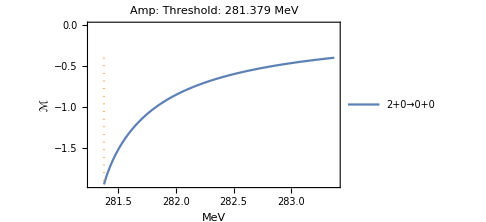
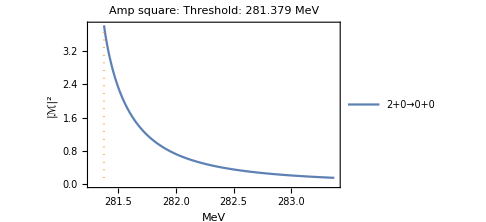

```mathematica
Row[{displayfunction1[Msumdat,{-0.1,2}],displayfunction2[Msumdat,{-0.1,2}]}]
```

```mathematica
Msumdat=Msum2[{80,60},{2,2,0,0},SRange->{10^-3,2,0.01}]
```

Wavefunction build complete.

M1=141.057  M2=141.057  M3=140.322  M4=140.322

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{{2,2,0,0},{141.057,141.057,140.322,140.322}},{{282.115,1.43541},{282.125,1.4211},{282.135,1.39874},{282.145,1.37513},{282.155,1.35134},{282.165,1.32773},{282.175,1.3045},{282.185,1.28171},{282.195,1.25942},{282.205,1.23764},{282.215,1.21633},{282.225,1.19565},{282.235,1.17543},{282.245,1.15571},{282.255,1.13648},{282.265,1.11774},{282.275,1.09946},{282.285,1.08163},{282.295,1.06424},{282.305,1.04728},{282.315,1.03073},{282.325,1.01458},{282.335,0.998816},{282.345,0.983428},{282.355,0.968405},{282.365,0.953733},{282.375,0.939403},{282.385,0.925404},{282.395,0.911724},{282.405,0.898356},{282.415,0.885288},{282.425,0.872513},{282.435,0.860021},{282.445,0.847803},{282.455,0.835852},{282.465,0.824159},{282.475,0.812718},{282.485,0.80152},{282.495,0.790558},{282.505,0.779827},{282.515,0.769319},{282.525,0.759027},{282.535,0.748947},{282.545,0.739072},{282.555,0.729396},{282.565,0.719915},{282.575,0.710622},{282.585,0.701512},{282.595,0.692581},{282.605,0.683824},{282.615,0.675236},{282.625,0.666814},{282.635,0.658551},{282.645,0.650445},{282.655,0.642492},{282.665,0.634687},{282.675,0.627027},{282.685,0.619508},{282.695,0.612126},{282.705,0.604879},{282.715,0.597763},{282.725,0.590774},{282.735,0.58391},{282.745,0.577167},{282.755,0.570544},{282.765,0.564036},{282.775,0.557641},{282.785,0.551356},{282.795,0.54518},{282.805,0.539109},{282.815,0.53314},{282.825,0.527273},{282.835,0.521503},{282.845,0.51583},{282.855,0.510251},{282.865,0.504763},{282.875,0.499365},{282.885,0.494055},{282.895,0.488831},{282.905,0.483691},{282.915,0.478633},{282.925,0.473655},{282.935,0.468757},{282.945,0.463935},{282.955,0.459188},{282.965,0.454515},{282.975,0.449915},{282.985,0.445385},{282.995,0.440925},{283.005,0.436532},{283.015,0.432206},{283.025,0.427945},{283.035,0.423747},{283.045,0.419613},{283.055,0.415539},{283.065,0.411525},{283.075,0.407571},{283.085,0.403674},{283.095,0.399833},{283.105,0.396048},{283.115,0.392317},{283.125,0.38864},{283.135,0.385015},{283.145,0.381441},{283.155,0.377917},{283.165,0.374443},{283.175,0.371017},{283.185,0.367639},{283.195,0.364308},{283.205,0.361022},{283.215,0.357781},{283.225,0.354584},{283.235,0.351431},{283.245,0.34832},{283.255,0.345239},{283.265,0.342222},{283.275,0.339234},{283.285,0.336286},{283.295,0.333372},{283.305,0.330505},{283.315,0.327671},{283.325,0.324874},{283.335,0.322113},{283.345,0.319387},{283.355,0.316697},{283.365,0.314041},{283.375,0.311418},{283.385,0.308829},{283.395,0.306272},{283.405,0.303748},{283.415,0.301255},{283.425,0.298792},{283.435,0.29636},{283.445,0.293959},{283.455,0.291587},{283.465,0.289243},{283.475,0.286929},{283.485,0.284642},{283.495,0.282383},{283.505,0.280151},{283.515,0.277946},{283.525,0.275767},{283.535,0.273614},{283.545,0.271487},{283.555,0.269384},{283.565,0.267306},{283.575,0.265253},{283.585,0.263223},{283.595,0.261217},{283.605,0.259234},{283.615,0.257273},{283.625,0.255335},{283.635,0.25342},{283.645,0.251526},{283.655,0.249653},{283.665,0.247801},{283.675,0.245971},{283.685,0.244161},{283.695,0.24237},{283.705,0.2406},{283.715,0.23885},{283.725,0.237118},{283.735,0.235406},{283.745,0.233712},{283.755,0.232037},{283.765,0.23038},{283.775,0.228741},{283.785,0.227119},{283.795,0.225515},{283.805,0.223928},{283.815,0.222358},{283.825,0.220805},{283.835,0.219268},{283.845,0.217747},{283.855,0.216242},{283.865,0.214753},{283.875,0.213279},{283.885,0.211821},{283.895,0.210378},{283.905,0.20895},{283.915,0.207536},{283.925,0.206137},{283.935,0.204752},{283.945,0.203381},{283.955,0.202024},{283.965,0.200681},{283.975,0.199351},{283.985,0.198035},{283.995,0.196731},{284.005,0.195441},{284.015,0.194164},{284.025,0.192899},{284.035,0.191647},{284.045,0.190407},{284.055,0.189179},{284.065,0.187963},{284.075,0.186759},{284.085,0.185566},{284.095,0.184385},{284.105,0.183216}}}

```mathematica
Row[{displayfunction1[Msumdat,{-0.1,2}],displayfunction2[Msumdat,{-0.1,2}]}]
```

-Graphics--Graphics-

```mathematica
Msumdat=Msum2[{80,60},{2,2,2,2},SRange->{10^-3,5,0.05}]
```

Wavefunction build complete.

M1=141.057  M2=141.057  M3=141.057  M4=141.057

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{{2,2,2,2},{141.057,141.057,141.057,141.057}},{{282.115,8.05985},{282.165,8.05718},{282.215,8.05452},{282.265,8.05186},{282.315,8.04921},{282.365,8.04655},{282.415,8.04389},{282.465,8.04124},{282.515,8.03858},{282.565,8.03593},{282.615,8.03328},{282.665,8.03063},{282.715,8.02798},{282.765,8.02534},{282.815,8.02269},{282.865,8.02005},{282.915,8.0174},{282.965,8.01476},{283.015,8.01212},{283.065,8.00948},{283.115,8.00684},{283.165,8.00421},{283.215,8.00157},{283.265,7.99894},{283.315,7.9963},{283.365,7.99367},{283.415,7.99104},{283.465,7.98841},{283.515,7.98578},{283.565,7.98316},{283.615,7.98053},{283.665,7.97791},{283.715,7.97529},{283.765,7.97266},{283.815,7.97004},{283.865,7.96742},{283.915,7.96481},{283.965,7.96219},{284.015,7.95958},{284.065,7.95696},{284.115,7.95435},{284.165,7.95174},{284.215,7.94913},{284.265,7.94652},{284.315,7.94391},{284.365,7.9413},{284.415,7.9387},{284.465,7.93609},{284.515,7.93349},{284.565,7.93089},{284.615,7.92829},{284.665,7.92569},{284.715,7.92309},{284.765,7.9205},{284.815,7.9179},{284.865,7.91531},{284.915,7.91271},{284.965,7.91012},{285.015,7.90753},{285.065,7.90494},{285.115,7.90235},{285.165,7.89977},{285.215,7.89718},{285.265,7.8946},{285.315,7.89202},{285.365,7.88943},{285.415,7.88685},{285.465,7.88427},{285.515,7.8817},{285.565,7.87912},{285.615,7.87654},{285.665,7.87397},{285.715,7.8714},{285.765,7.86882},{285.815,7.86625},{285.865,7.86368},{285.915,7.86112},{285.965,7.85855},{286.015,7.85598},{286.065,7.85342},{286.115,7.85086},{286.165,7.84829},{286.215,7.84573},{286.265,7.84317},{286.315,7.84062},{286.365,7.83806},{286.415,7.8355},{286.465,7.83295},{286.515,7.83039},{286.565,7.82784},{286.615,7.82529},{286.665,7.82274},{286.715,7.82019},{286.765,7.81764},{286.815,7.8151},{286.865,7.81255},{286.915,7.81001},{286.965,7.80747},{287.015,7.80493},{287.065,7.80239}}}

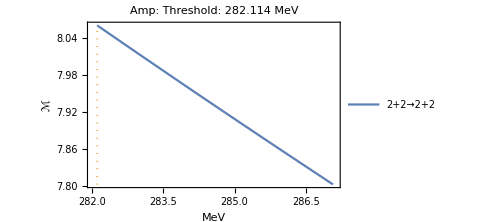
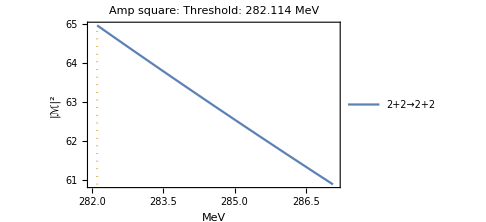

```mathematica
Row[{displayfunction1[Msumdat,{-0.1,5}],displayfunction2[Msumdat,{-0.1,5}]}]
```

```mathematica
Msumdat=Msum2[{80,60},{1,1,1,1},SRange->{10^-3,5,0.05}]
```

Wavefunction build complete.

M1=140.757  M2=140.757  M3=140.757  M4=140.757

{{{1,1,1,1},{140.757,140.757,140.757,140.757}},{{281.515,8.0431},{281.565,8.04043},{281.615,8.03776},{281.665,8.0351},{281.715,8.03244},{281.765,8.02977},{281.815,8.02711},{281.865,8.02445},{281.915,8.02179},{281.965,8.01914},{282.015,8.01648},{282.065,8.01382},{282.115,8.01117},{282.165,8.00852},{282.215,8.00587},{282.265,8.00322},{282.315,8.00057},{282.365,7.99792},{282.415,7.99528},{282.465,7.99263},{282.515,7.98999},{282.565,7.98735},{282.615,7.98471},{282.665,7.98207},{282.715,7.97943},{282.765,7.97679},{282.815,7.97416},{282.865,7.97152},{282.915,7.96889},{282.965,7.96626},{283.015,7.96363},{283.065,7.961},{283.115,7.95837},{283.165,7.95574},{283.215,7.95312},{283.265,7.95049},{283.315,7.94787},{283.365,7.94525},{283.415,7.94263},{283.465,7.94001},{283.515,7.93739},{283.565,7.93477},{283.615,7.93216},{283.665,7.92954},{283.715,7.92693},{283.765,7.92432},{283.815,7.92171},{283.865,7.9191},{283.915,7.91649},{283.965,7.91388},{284.015,7.91128},{284.065,7.90868},{284.115,7.90607},{284.165,7.90347},{284.215,7.90087},{284.265,7.89827},{284.315,7.89567},{284.365,7.89308},{284.415,7.89048},{284.465,7.88789},{284.515,7.8853},{284.565,7.8827},{284.615,7.88011},{284.665,7.87752},{284.715,7.87494},{284.765,7.87235},{284.815,7.86976},{284.865,7.86718},{284.915,7.8646},{284.965,7.86202},{285.015,7.85944},{285.065,7.85686},{285.115,7.85428},{285.165,7.8517},{285.215,7.84913},{285.265,7.84655},{285.315,7.84398},{285.365,7.84141},{285.415,7.83884},{285.465,7.83627},{285.515,7.8337},{285.565,7.83113},{285.615,7.82857},{285.665,7.826},{285.715,7.82344},{285.765,7.82088},{285.815,7.81832},{285.865,7.81576},{285.915,7.8132},{285.965,7.81064},{286.015,7.80809},{286.065,7.80553},{286.115,7.80298},{286.165,7.80043},{286.215,7.79788},{286.265,7.79533},{286.315,7.79278},{286.365,7.79023},{286.415,7.78769},{286.465,7.78514}}}

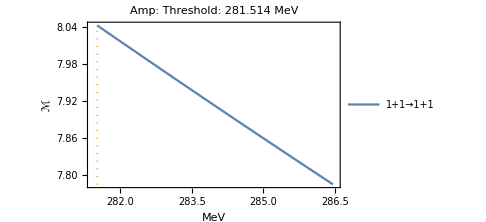
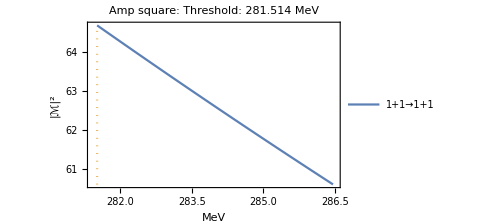

```mathematica
Row[{displayfunction1[Msumdat,{-0.1,5}],displayfunction2[Msumdat,{-0.1,5}]}]
```

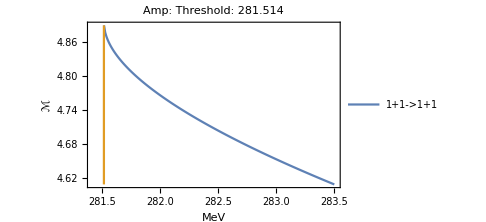
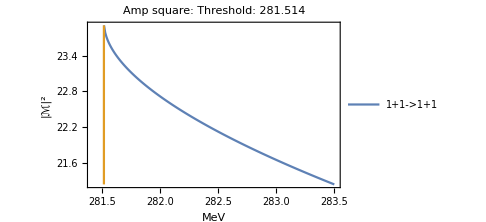

```mathematica
Row[{ListPlot[{Select[Re@Msumdat[[2]],#∈Reals&],{{Msumdat[[1,1]]+Msumdat[[1,2]],Last[Msumdat[[2]]][[2]]},{Msumdat[[1,1]]+Msumdat[[1,2]],First[Msumdat[[2]]][[2]]}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,Msumdat[[1,1]]+Msumdat[[1,2]]+2},All},Joined->True,PlotLabel->"Amp: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium,PlotLegends->Placed[LineLegend[{"1+1->1+1"},LegendLayout->{"Column",1}(*,LegendMarkerSize->20*),LegendMargins->3,LegendFunction->"Frame"],{Right,Top}],Frame->True,FrameLabel->{"MeV","ℳ"}],
ListPlot[{Transpose@{Transpose[Msumdat[[2]]][[1]],(Transpose[Msumdat[[2]]][[2]])^2},{{Msumdat[[1,1]]+Msumdat[[1,2]],(Last[Msumdat[[2]]][[2]])^2},{Msumdat[[1,1]]+Msumdat[[1,2]],(First[Msumdat[[2]]][[2]])^2}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,Msumdat[[1,1]]+Msumdat[[1,2]]+2},All},Joined->True,PlotLabel->"Amp square: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium,PlotLegends->Placed[LineLegend[{"1+1->1+1"},LegendLayout->{"Column",1}(*,LegendMarkerSize->20*),LegendMargins->3,LegendFunction->"Frame"],{Right,Top}],Frame->True,FrameLabel->{"MeV","|ℳ|^2"}]}]
```

```mathematica
Msumdat=Msum2[{80,60},{1,1,0,0},SRange->{10^-3,2,0.01}]
```

Wavefunction build complete.

M1=140.757  M2=140.757  M3=140.322  M4=140.322

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{{1,1,0,0},{140.757,140.757,140.322,140.322}},{{281.515,2.36494},{281.525,2.37855},{281.535,2.36313},{281.545,2.34134},{281.555,2.31689},{281.565,2.29118},{281.575,2.26493},{281.585,2.2385},{281.595,2.21215},{281.605,2.18602},{281.615,2.1602},{281.625,2.13475},{281.635,2.10972},{281.645,2.08512},{281.655,2.06098},{281.665,2.03731},{281.675,2.01409},{281.685,1.99134},{281.695,1.96905},{281.705,1.94722},{281.715,1.92583},{281.725,1.90487},{281.735,1.88435},{281.745,1.86424},{281.755,1.84454},{281.765,1.82524},{281.775,1.80634},{281.785,1.78781},{281.795,1.76965},{281.805,1.75185},{281.815,1.7344},{281.825,1.71729},{281.835,1.70051},{281.845,1.68406},{281.855,1.66791},{281.865,1.65208},{281.875,1.63654},{281.885,1.6213},{281.895,1.60633},{281.905,1.59164},{281.915,1.57722},{281.925,1.56306},{281.935,1.54915},{281.945,1.53549},{281.955,1.52207},{281.965,1.50888},{281.975,1.49592},{281.985,1.48319},{281.995,1.47067},{282.005,1.45836},{282.015,1.44626},{282.025,1.43436},{282.035,1.42266},{282.045,1.41115},{282.055,1.39982},{282.065,1.38868},{282.075,1.37772},{282.085,1.36693},{282.095,1.35631},{282.105,1.34585},{282.115,1.33556},{282.125,1.32543},{282.135,1.31545},{282.145,1.30562},{282.155,1.29594},{282.165,1.28641},{282.175,1.27701},{282.185,1.26776},{282.195,1.25864},{282.205,1.24965},{282.215,1.24079},{282.225,1.23206},{282.235,1.22345},{282.245,1.21496},{282.255,1.2066},{282.265,1.19834},{282.275,1.19021},{282.285,1.18218},{282.295,1.17426},{282.305,1.16645},{282.315,1.15875},{282.325,1.15114},{282.335,1.14364},{282.345,1.13624},{282.355,1.12893},{282.365,1.12172},{282.375,1.1146},{282.385,1.10757},{282.395,1.10064},{282.405,1.09379},{282.415,1.08702},{282.425,1.08034},{282.435,1.07375},{282.445,1.06723},{282.455,1.0608},{282.465,1.05444},{282.475,1.04816},{282.485,1.04196},{282.495,1.03583},{282.505,1.02977},{282.515,1.02379},{282.525,1.01787},{282.535,1.01203},{282.545,1.00624},{282.555,1.00054},{282.565,0.994896},{282.575,0.989316},{282.585,0.983799},{282.595,0.978344},{282.605,0.972951},{282.615,0.967617},{282.625,0.962343},{282.635,0.957128},{282.645,0.951969},{282.655,0.946867},{282.665,0.94182},{282.675,0.936828},{282.685,0.93189},{282.695,0.927004},{282.705,0.92217},{282.715,0.917387},{282.725,0.912655},{282.735,0.907972},{282.745,0.903338},{282.755,0.898751},{282.765,0.894212},{282.775,0.88972},{282.785,0.885273},{282.795,0.880872},{282.805,0.876514},{282.815,0.872201},{282.825,0.86793},{282.835,0.863703},{282.845,0.859516},{282.855,0.855371},{282.865,0.851267},{282.875,0.847203},{282.885,0.843178},{282.895,0.839191},{282.905,0.835244},{282.915,0.831333},{282.925,0.827461},{282.935,0.823624},{282.945,0.819824},{282.955,0.81606},{282.965,0.81233},{282.975,0.808635},{282.985,0.804975},{282.995,0.801348},{283.005,0.797754},{283.015,0.794193},{283.025,0.790665},{283.035,0.787168},{283.045,0.783703},{283.055,0.780268},{283.065,0.776865},{283.075,0.773491},{283.085,0.770148},{283.095,0.766833},{283.105,0.763548},{283.115,0.760292},{283.125,0.757063},{283.135,0.753863},{283.145,0.75069},{283.155,0.747544},{283.165,0.744426},{283.175,0.741333},{283.185,0.738267},{283.195,0.735227},{283.205,0.732212},{283.215,0.729222},{283.225,0.726257},{283.235,0.723317},{283.245,0.720401},{283.255,0.717509},{283.265,0.71464},{283.275,0.711795},{283.285,0.708973},{283.295,0.706174},{283.305,0.703398},{283.315,0.700643},{283.325,0.697911},{283.335,0.6952},{283.345,0.692511},{283.355,0.689843},{283.365,0.687196},{283.375,0.68457},{283.385,0.681964},{283.395,0.679378},{283.405,0.676813},{283.415,0.674267},{283.425,0.671741},{283.435,0.669234},{283.445,0.666746},{283.455,0.664277},{283.465,0.661827},{283.475,0.659395},{283.485,0.656981},{283.495,0.654585},{283.505,0.652208}}}

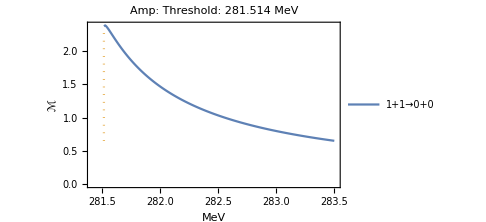
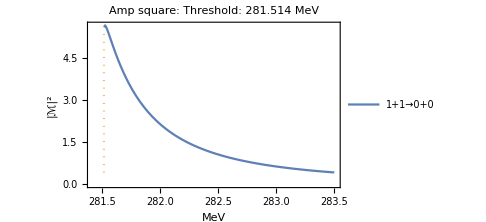

```mathematica
Row[{displayfunction1[Msumdat,{-0.1,2}],displayfunction2[Msumdat,{-0.1,2}]}]
```

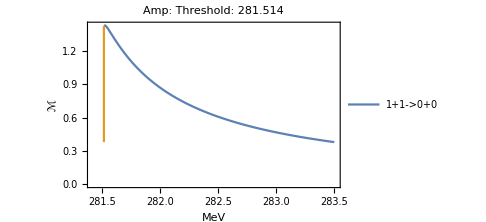
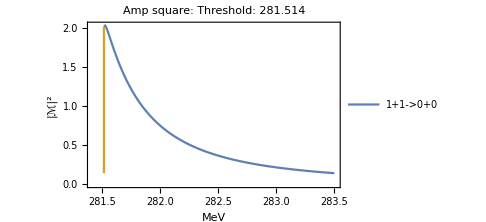

```mathematica
Row[{ListPlot[{Select[Re@Msumdat[[2]],#∈Reals&],{{Msumdat[[1,1]]+Msumdat[[1,2]],Last[Msumdat[[2]]][[2]]},{Msumdat[[1,1]]+Msumdat[[1,2]],First[Msumdat[[2]]][[2]]}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,Msumdat[[1,1]]+Msumdat[[1,2]]+2},All},Joined->True,PlotLabel->"Amp: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium,PlotLegends->Placed[LineLegend[{"1+1->0+0"},LegendLayout->{"Column",1}(*,LegendMarkerSize->20*),LegendMargins->3,LegendFunction->"Frame"],{Right,Top}],Frame->True,FrameLabel->{"MeV","ℳ"}],
ListPlot[{Transpose@{Transpose[Msumdat[[2]]][[1]],(Transpose[Msumdat[[2]]][[2]])^2},{{Msumdat[[1,1]]+Msumdat[[1,2]],(Last[Msumdat[[2]]][[2]])^2},{Msumdat[[1,1]]+Msumdat[[1,2]],(First[Msumdat[[2]]][[2]])^2}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,Msumdat[[1,1]]+Msumdat[[1,2]]+2},All},Joined->True,PlotLabel->"Amp square: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium,PlotLegends->Placed[LineLegend[{"1+1->0+0"},LegendLayout->{"Column",1}(*,LegendMarkerSize->20*),LegendMargins->3,LegendFunction->"Frame"],{Right,Top}],Frame->True,FrameLabel->{"MeV","|ℳ|^2"}]}]
```

### Debug

```mathematica
Block[{mQ=80,mq=60},m1=mQ;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determineϕx[m1,m2,β,Nx];
ΦB[x_]=ϕxB;
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
ΦB[x_]=ϕxB;
}
];
Print["Wavefunction build complete."];
(*Print[ϕn[#][Φ][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];]
```

Wavefunction build complete.

```mathematica
ω1S[(M1+M2+0.1)^2][M1,M2,M3,M4]
ω2S[(M1+M2+0.001)^2][M1,M2,M3,M4]
```

0.948011

0.994675

```mathematica
Block[{ω1=0.907479105147823,ω2,Sen},ω2=ω2p[ω1][M1,M2,M3,M4];Sen=√(Sω1[ω1][M1,M2,M3,M4]);If[ω2∈Reals&&Sen∈Reals,Print["ω1=",ω1,"    ω2=",ω2];{Sen,MVG[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]+MHG[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]},Print["Overflow: ω1=",ω1]]]
```

ω1=0.907479    ω2=0.814958

{282.114,0.856536}

```mathematica
M1
M3
```

141.057

140.322

```mathematica
ω2fz[0.1][M1,M2,M3,M4]
```

9.11815

```mathematica
Sω1[ω1_]=Interpolation[Table[{ω1fz[z][M1,M2,M3,M4],√(S[z][M1,M2])},{z,0.00001,1,0.01}]][ω1];
```

```mathematica
FindMinimum[Sω1[ω1],{ω1,0.9}]
```

InterpolatingFunction::dmval: Input value {1.4} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{282.114,{ω1→0.906906}}

```mathematica
FindMinimum[Sω1[ω][M1,M2,M3,M4],{ω,0.5}]
```

{80435.2,{ω→0.873921}}

```mathematica
NMinimize[Sω1[ω][M1,M2,M3,M4],ω]
```

NMinimize::cvdiv: Failed to converge to a solution. The function may be unbounded.

{-4.01713×10^39,{ω→-4.95306×10^-36}}

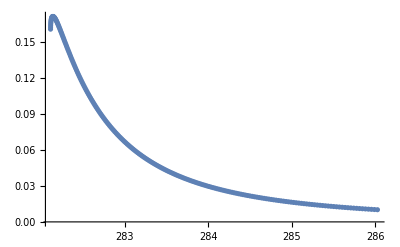

```mathematica
ListPlot[Table[{Sω1[x],Interpolation[list][x]},{x,0.7,0.9063125424888346,0.001}]](*This shows that with only MVG there can be a peak*)
```

```mathematica
FindRoot[ω1fz[z][M1,M2,M3,M4]==0.5,{z,0.5}]
```

{z→0.335635}

```mathematica
√(S[0.335635][M1,M2])
```

298.715

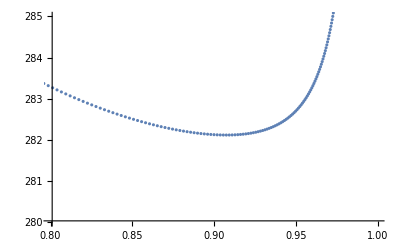

```mathematica
ListPlot[Table[{ω1fz[z][M1,M2,M3,M4],√(S[z][M1,M2])},{z,0.3,0.95,0.001}],PlotRange->{{0.8,0.9999},{280,285}}]
```

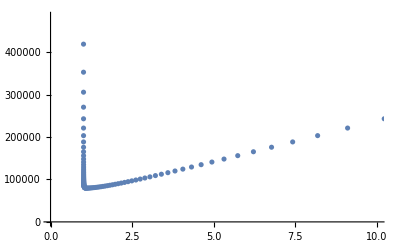

```mathematica
ListPlot[Table[{ω1fz[z][M1,M2,M3,M4],√(S[z][M1,M2])},{z,0.00001,1,0.01}]]
```

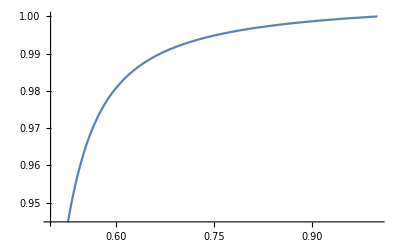

```mathematica
Plot[ω1fz[z][M1,M2,M3,M4],{z,0.5,1}]
```

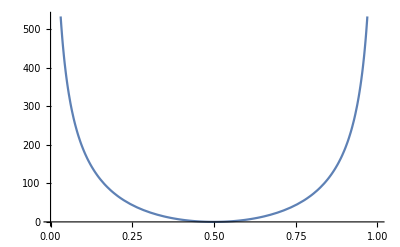

```mathematica
Plot[√(S[z][M1,M2])-M1-M2,{z,0,1}]
```

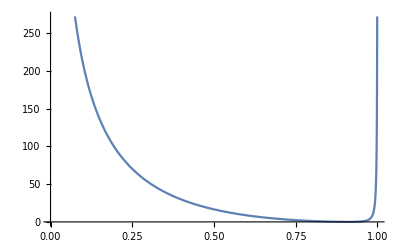

```mathematica
Plot[√(S[zfω[ω1][M1,M2,M3,M4]][M1,M2])-M1-M2,{ω1,0,1}]
```

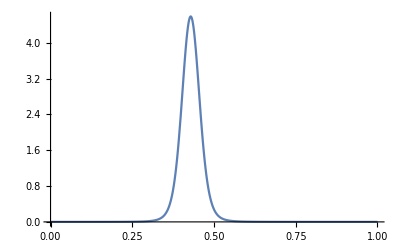

```mathematica
Plot[-ϕ3[1-y],{y,0,1},PlotRange->All]
```

```mathematica
g=1;
```

```mathematica
ω2n[0.5][M1,M2,M3,M4]
```

0.489712

```mathematica
Block[{ω1=0.4,ω2},ω2=ω2n[ω1][M1,M2,M3,M4];4 g^2 ω2(1+ω2-ω1) NIntegrate[1/(y ω2-x(1+ω2-ω1)-ω1)^2 ϕ1[x]ϕ2[(y ω2)/ω1]ϕ3[ω1-ω2+(1-ω1+ω2)x]ϕ4[y],{x,0,1},{y,0,1}]]//AbsoluteTiming
```

{82.5583,0.00115006}

```mathematica
Block[{ω1=0.4,ω2},ω2=ω2n[ω1][M1,M2,M3,M4];4 g^2 ω2(1+ω2-ω1) NIntegrate[1/(y ω2-x(1+ω2-ω1))^2 ϕ1[x]ϕ2[(y ω2)/ω1]ϕ3[ω1-ω2+x(1+ω2-ω1)]ϕ4[y],{x,0,1},{y,0,1},Method->"LocalAdaptive"]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.19947,0.503909}. NIntegrate obtained 3.70352×10^-7 and 5.01609×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.19947,0.503913}. NIntegrate obtained 2.21383×10^-7 and 1.4234×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.19947,0.503917}. NIntegrate obtained 1.1664×10^-6 and 2.72411×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

$Aborted

```mathematica
Block[{ω1=0.4,ω2},ω2=ω2n[ω1][M1,M2,M3,M4];4 g^2 ω2(1+ω2-ω1) NIntegrate[1/(y ω2-x(1+ω2-ω1))^2 ϕ1[x]ϕ2[(y ω2)/ω1]ϕ3[ω1-ω2+x(1+ω2-ω1)]ϕ4[y],{x,0,1},{y,0,1},Method->"AdaptiveMonteCarlo"]]//AbsoluteTiming
```

$Aborted

```mathematica
Block[{ω1=0.49},MVG[ω1,ω2n[ω1][M1,M2,M3,M4]][ϕ1,ϕ2,ϕ3,ϕ4]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.000293161

```mathematica
Block[{ω1=0.55},MVG[ω1,ω2n[ω1][M1,M2,M3,M4]][ϕ1,ϕ2,ϕ3,ϕ4]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.000637646